При gb = 1.4 10^-11, bin = 6 10^-4 эффективность 90%

5.70487

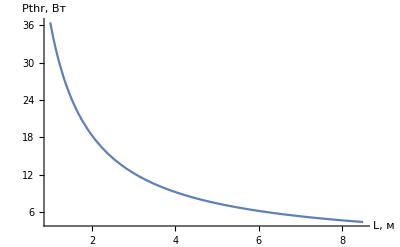

```mathematica
Clear["Global`*"]
(σ=Import[NotebookDirectory[]<>"CrossSection.xls",{"DataLegacy"}][[1,5;;,{12,15,16}]])//TableForm;

(*ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]*)

σe=Interpolation[σ[[All,{1,2}]],InterpolationOrder->1];
σa=Interpolation[σ[[All,{1,3}]],InterpolationOrder->1];
gb =N[5. 10^-11]; (*m/W*) (*в Агравале 5, но из вступления в статье получается в два раза меньше*)
d=10.5 10^-6;(*m*)
A=N[(π d^2)/4];(*m^2*)
L1= 2.; (*m*)
L2=3.5;
L3=1.;
L=L1+L2+L3; (*m*)
α =6 10^-3;(*1/m*)(* ~22dB/km *) (*Smith1972 pp4*) (*5*)
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=5400;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
(*Nz[z_]:=HeavisidePi[(z-(L1+L2/2))/L2];*)
Nz[z_]=(HeavisideTheta[z-L1])(1-HeavisideTheta[z-(L1+L2)]);
NN0[z_]=NN Nz[z];
h=6.63 10^-34;(*Планк*)
λp=1030;(*нм*)
λs=1064;(*нм*)
(*λ = λs;(*m*)*)
Ps=A h c/(λs 10^-9);
Pp=A h c/(λp 10^-9);
σp12=σa[λp];
σp21=σe[λp];
Ps0=0.180;
(*Δνb=20 10^6; (*Hz*)
Tb=N[1/(π Δνb)]; (*с*)*)
P1030Table = {0.98,1.74,2.5,3.24,4.0,4.7,5.23,6.25,7.2,8.2,9.25,10.4,11.06,11.6,11.8,12.2,12.6,13.5,14.5,15.0,15.95,16.85,17.54,18.06,18.23,18.8,20.3,21.2,22.4,23.3,24.25};
(BR193=Import[NotebookDirectory[]<>"Книга1.xlsx",{"DataLegacy"}][[1,4;;,{3,12}]])//TableForm;
BR193[[All,2]]=BR193[[All,2]]/1000.-0.2;
bin= 1. 10^-6;
LE[L_]:=1/α(1-Exp[-α L]);
Pth[L_]:=21*A/(gb LE[L]);
Pth[6.5]
Plot[Pth[L],{L,1,8.5},AxesOrigin->{1,0},PlotRange->All,AxesLabel->{"L, м","Pthr, Вт"}]
```

```mathematica
Δν=13.; (*GHz*)
λS[λ_]:=(c λ)/(c-Δν λ);(*нм*)
PS[λ_]:=(A h c)/(λS[λ] 10^-9);
σSp12=σa[λS[λp]];
σSp21=σe[λS[λp]];
σSs12=σa[λS[λs]];
σSs21=σe[λS[λs]];
eqns1={
0==ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σa[λs] N1[z]-σe[λs] N2[z])+ρs2[z](σSp12 N1[z]-σSp21 N2[z])+ρs1[z](σSs12 N1[z]-σSs21 N2[z])-N2[z]/τ,
ρs'[z]==ρs[z](σe[λs] N2[z]-σa[λs] N1[z])-α*ρs[z]-(gb PS[λs])/A ρs[z] ρs1[z],
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z])-α*ρp[z]-(gb PS[λp])/A ρp[z] ρs2[z],
ρs1'[z]==(-gb Ps)/A ρs[z]ρs1[z]+α ρs1[z]-ρs1[z](σSs21 N2[z]-σSs12 N1[z]),
ρs2'[z]==(-gb Pp)/A ρp[z]ρs2[z]+α ρs2[z]-ρs2[z](σSp21 N2[z]-σSp12 N1[z]),
N1[z]+N2[z]==NN0[z]};

sol0=Solve[eqns1[[{1,6}]],{N1[z],N2[z]}][[1]];
eqns2=Simplify[eqns1[[{2,3,4,5}]]/.%];
sol[Ppump_]:=NDSolve[{eqns2,ρs1[L]==bin ρs[L], ρs2[L]==bin ρp[L],Pp ρp[0]==Ppump,Ps ρs[0]==Ps0},{ρp,ρs,ρs1,ρs2},{z,0,L},AccuracyGoal->8][[1]];
```

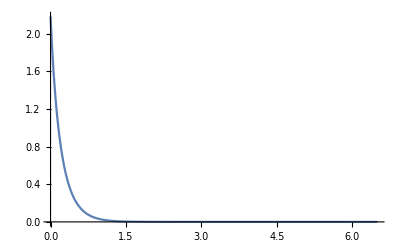

```mathematica
Plot[Evaluate[PS[λp] ρs2[z]/.sol[10.]],{z,0,L},PlotRange->All]
```

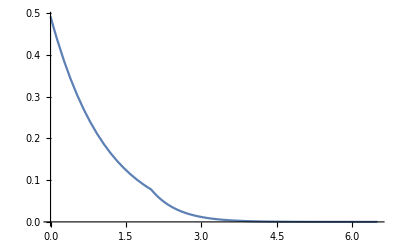

```mathematica
Plot[Evaluate[PS[λs] ρs1[z]/.sol[10.]],{z,0,L},PlotRange->All]
```

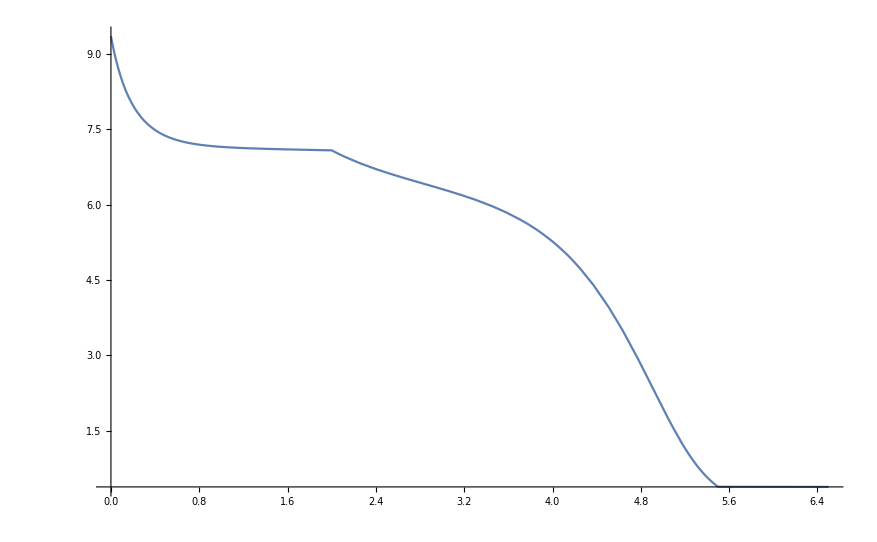

```mathematica
Plot[Evaluate[Pp ρp[z]/.sol[10.]],{z,0,L},PlotRange->All]
```

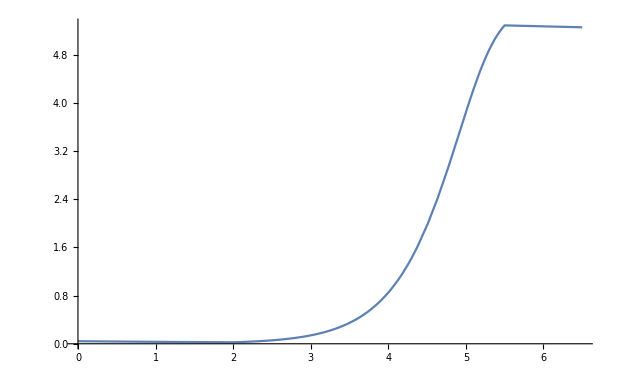

```mathematica
Plot[Evaluate[Ps ρs[z]/.sol[10.]],{z,0,L},PlotRange->All]
```

```mathematica
Plot[Evaluate[(N2[z]/.sol0)/.sol[10.]],{z,0,L},PlotRange->All]
```

-Graphics-

```mathematica
Plot[Evaluate[(N1[z]/.sol0)/.sol[10.]],{z,0,L},PlotRange->All]
```

-Graphics-

```mathematica
(N2[1.]/.sol0)/.sol[10.]
```

N2[1.]

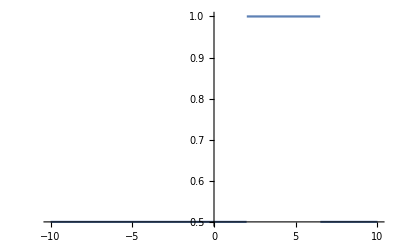

```mathematica
Plot[(1-HeavisideTheta[x-6.5]+HeavisideTheta[x-2.])0.5,{x,-10,10},PlotRange->All]
```

```mathematica
Plot[NN0[z],{z,0,L}]
```

-Graphics-

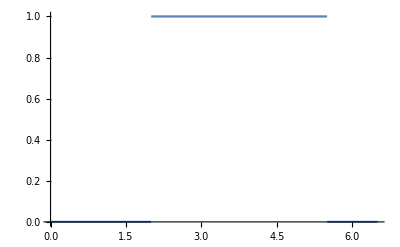

```mathematica
Plot[HeavisidePi[(z-(L1+L2/2))/L2],{z,0,L}]
```

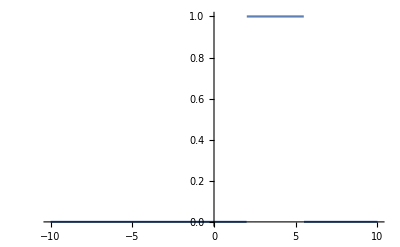

```mathematica
Plot[(HeavisideTheta[z-L1])(1-HeavisideTheta[z-(L1+L2)]),{z,-10,10}]
```

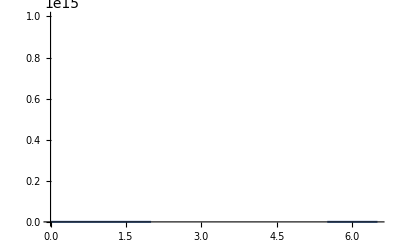

```mathematica
Plot[NN0[z],{z,0,L}]
```

```mathematica
NN0[1.]
```

0.